```mathematica
Bv0prob={0.9639,0.03587,0.00017,0.00001};
Total[Bv0prob]
```

0.99995

```mathematica
Av0prob={0.986,0.0139,0.00002};
Total[Av0prob]
```

0.99992

```mathematica
Bv1prob={0.1137,0.8169,0.0739,0.00611};
Total[Bv1prob]
```

1.01061

```mathematica
list0={}; (*Just 905 lasers, assume that spin splitting is closed.*)
For[j=0,j<1000,
state=0;
count=0;
For[i=0,i<500000,
Which[state==0,state=RandomChoice[Bv0prob->{0,1,2,3},1][[1]],
state==1,count=i;i=10^10,
state==2,count=i;i=10^10,
state==3,count=i;i=10^10];
i++];
list0=Append[list0,count];j++]
N[Mean[list0]]
```

27.22

```mathematica
list1={};(*905 lasers + 1 set of repumps, assume that spin splitting is closed.*)
For[j=0,j<1000,
state=0;
count=0;
For[i=0,i<500000,
Which[state==0,state=RandomChoice[Bv0prob->{0,1,2,3},1][[1]],
state==1,state=RandomChoice[Bv0prob->{0,1,2,3},1][[1]],
state==2,count=i;i=10^10,
state==3,count=i;i=10^10];
i++];
list1=Append[list1,count];j++]
N[Mean[list1]]
```

5492.76

```mathematica
list2={};(*905 lasers + both repumps, assume that spin splitting is closed.*)
For[j=0,j<1000,
state=0;
count=0;
For[i=0,i<500000,
Which[state==0,state=RandomChoice[Bv0prob->{0,1,2,3},1][[1]],
state==1,state=RandomChoice[Bv0prob->{0,1,2,3},1][[1]],
state==2,state=RandomChoice[Bv1prob->{0,1,2,3},1][[1]],
state==3,count=i;i=10^10];
i++];
list2=Append[list2,count];j++]
N[Mean[list2]]
```

87784.8

```mathematica
olist0=Sort[list0];
cdf0={};
For[k=1000,k<5000,
cdf0=Append[cdf0,{k,(1000-Total[BinCounts[olist0,{0,k,2000}]])/1000}];k=k+10];
olist1=Sort[list1];
cdf1={};
For[k=1000,k<500000,
cdf1=Append[cdf1,{k,(1000-Total[BinCounts[olist1,{0,k,2000}]])/1000}];k=k+5000];
olist2=Sort[list2];
cdf2={};
For[k=1000,k<500000,
cdf2=Append[cdf2,{k,(1000-Total[BinCounts[olist2,{0,k,2000}]])/1000}];k=k+5000]
```

```mathematica
N[Median[olist0]]
N[Median[olist1]]
N[Median[olist2]]
```

19.

3973.

61246.

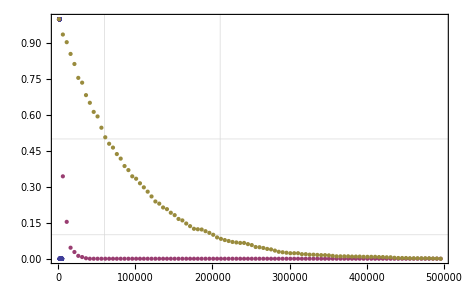

```mathematica
Show[ListPlot[{cdf0,cdf1,cdf2},GridLines->{{60000,210000},{0.1,0.5}},Frame->True]]
```

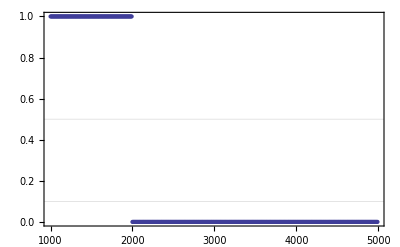

```mathematica
Show[ListPlot[cdf0,GridLines->{{60000,210000},{0.1,0.5}},Frame->True]]
```